## Python Code for obtain Penrose Encoding of a TM.

```mathematica
FindExternalEvaluators["Python"]
```

```mathematica
session=StartExternalSession["Python"]
```

ExternalSessionObject[…]

```mathematica
ExternalEvaluate[session,"file"]
```

## Mathematica Implementation for Visualization

```mathematica
MT=Import["C:\\Users\\emman\\Downloads\\universal (7).txt"];
```

```mathematica
MT=StringDelete[StringSplit[Text[MT]⟦1⟧,","],{"[","]","'", " "}];
```

```mathematica
ClearAll[multiGraph2]
multiGraph2[vl_,elist_,elabels_,estyles_,o:OptionsPattern[Graph]]:=Module[{esf,edges,labels,styles,sorted=Transpose@SortBy[Transpose[{elist,elabels,estyles}],{PositionIndex[vl]@#[[1,1]]&,PositionIndex[vl]@#[[1,2]]&}]},{edges,labels,styles}={sorted[[1]],##&@@(RotateRight/@sorted[[2;;]])};
esf={First[styles=RotateLeft[styles]],GraphElementData["Arrow", "ArrowSize"->0.01][##]/. Arrowheads[ah_]:>Arrowheads[Append[ah,{.0003,.7,Graphics[Text[Framed[First[labels=RotateLeft[labels]],FrameStyle->None,Background->White]]]}]]}&;
Graph[vl,edges,EdgeShapeFunction->esf,o]]
```

```mathematica
tabla3=ParallelTable[{{(StringSplit[MT[[i]],"->"][[1]]//Characters)[[1;;-2]]//StringJoin },{((StringSplit[MT[[i]],"->"][[1]]//Characters)[[1;;-2]]//StringJoin )->((StringSplit[MT[[i]],"->"][[2]]//Characters)[[;;-3]]//StringJoin)},{StringJoin[(StringSplit[MT[[i]],"->"][[1]]//Characters)//Last,(StringSplit[MT[[i]],"->"][[2]]//Characters)[[-2]],(StringSplit[MT[[i]],"->"][[2]]//Characters)//Last]}},{i,1,Length[MT]}];
```

```mathematica
fn=ParallelTable[{{FromDigits[(StringSplit[MT[[i]],"->"][[1]]//Characters)[[1;;-2]]//StringJoin ,2]},{FromDigits[((StringSplit[MT[[i]],"->"][[1]]//Characters)[[1;;-2]]//StringJoin ),2]->FromDigits[((StringSplit[MT[[i]],"->"][[2]]//Characters)[[;;-3]]//StringJoin),2]},{StringJoin[(StringSplit[MT[[i]],"->"][[1]]//Characters)//Last,(StringSplit[MT[[i]],"->"][[2]]//Characters)[[-2]],(StringSplit[MT[[i]],"->"][[2]]//Characters)//Last]}},{i,1,Length[MT]}];
```

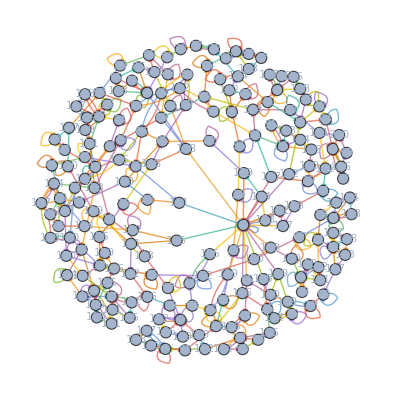

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
styles=ColorData[97]/@Range[Length[tabla3[[;;,3]]]];
multiGraph2[Flatten@Gather[(fn[[;;,1]]//Flatten)//DeleteDuplicates],fn[[;;,2]]//Flatten,fn[[;;,3]]//Flatten,styles,VertexSize->1,VertexLabels->Placed["Name",Center],ImageSize->Full, GraphLayout->"GravityEmbedding"]
```

## Pruebas anteriores

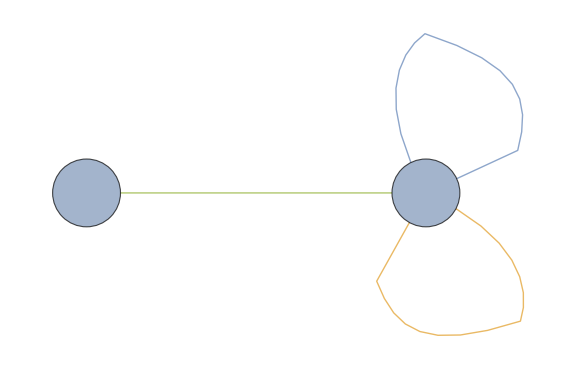

Rule::rhs: Pattern paclet:ref/FindExternalEvaluators appears on the right-hand side of rule RefLink[FindExternalEvaluators,paclet:ref/FindExternalEvaluators][]→-RefLink[FindExternalEvaluators,paclet:ref/FindExternalEvaluators][].

Even

```mathematica
multiGraph2[Flatten@Gather[(tabla3[[;;,1]]//Flatten)//DeleteDuplicates],tabla3[[;;,2]]//Flatten,tabla3[[;;,3]]//Flatten,styles,VertexSize->Medium,VertexLabels->Placed["Name",Center],ImageSize->Large]
```